```mathematica
Get["path-integrals.m"];
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
haywardVGMinus4 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,5}]);
haywardVGMinus3 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,5}]);
haywardVGMinus2 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,5}]);
haywardVGMinus1 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,5}]);
Clear[pints]
```

```mathematica
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX VG XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
(*XXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX*)
```

```mathematica
fitVar = 1;
time = 0.05;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
start= 0.1;
```

0.984642

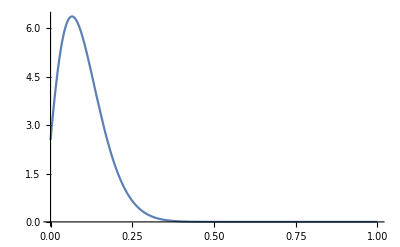

```mathematica
neutAUC = NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
Plot[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}], {y,0,1}]
```

```mathematica
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, start+Ψ,1}];
```

```mathematica
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
If[Length[thresh] != 1,Throw[{}]];
```

```mathematica
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
```

0.192309

```mathematica
pNeutFix +  NIntegrate[Evaluate[Kimura[x,y,t,50]/. {x->start, t->time}],{y, 0,start+Ψ}]
```

0.989995

```mathematica
(***********************)
(******* VG = 0.1 *******)
(***********************)
```

```mathematica
Do[Clear[totalP, Pdetected];
Print[selCoef,":"];
totalP = NIntegrate[Evaluate[haywardVGMinus1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.1,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardVGMinus1/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.1,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[0.1],".csv"], {{selCoef,0.1,start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0.0005,0.001,0.005, 0.01}}
]
```

0.0005:

0.984883 xxxx 0.0102081

0.001:

0.985122 xxxx 0.0104146

0.005:

0.986899 xxxx 0.0122093

0.01:

0.987958 xxxx 0.0147992

```mathematica
(************************)
(******* VG = 0.01 *******)
(************************)
```

```mathematica
Do[Clear[totalP, Pdetected];
Print[selCoef,":"];
totalP = NIntegrate[Evaluate[haywardVGMinus2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.01,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardVGMinus2/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.01,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[0.01],".csv"], {{selCoef,0.01,start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0.0005,0.001,0.005, 0.01}}
]
```

0.0005:

0.985284 xxxx 0.0109261

0.001:

0.985903 xxxx 0.0119198

0.005:

0.990115 xxxx 0.0230956

0.01:

0.993827 xxxx 0.0483963

```mathematica
(*************************)
(******* VG = 0.001 *******)
(*************************)
```

```mathematica
Do[Clear[totalP, Pdetected];
Print[selCoef,":"];
totalP = NIntegrate[Evaluate[haywardVGMinus3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.001,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardVGMinus3/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.001,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[0.001],".csv"], {{selCoef,0.001,start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0.0005,0.001,0.005, 0.01}}
]
```

0.0005:

0.985382 xxxx 0.0111735

0.001:

0.986091 xxxx 0.0124581

0.005:

0.990785 xxxx 0.028104

0.01:

0.994678 xxxx 0.067547

```mathematica
(**************************)
(******* VG = 0.0001 *******)
(**************************)
```

```mathematica
Do[Clear[totalP, Pdetected];
Print[selCoef,":"];
totalP = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.0001,  W->fitVar}],{y, 0,1}];
Pdetected = NIntegrate[Evaluate[haywardVGMinus4/.{x->start,t -> time, α->selCoef,Λ -> jumpSize, Ne->selectedNe, VG->0.0001,  W->fitVar}],{y, start+Ψ,1}];
Print[totalP, " xxxx ", Pdetected];
Export[StringJoin["pDetection_","alpha",ToString[selCoef], "_VG",ToString[0.0001],".csv"], {{selCoef,0.0001,start,Ψ,totalP,Pdetected}}, "csv"],
{selCoef, {0.0005,0.001,0.005, 0.01}}
]
```

0.0005:

0.985393 xxxx 0.011203

0.001:

0.986112 xxxx 0.0125228

0.005:

0.990858 xxxx 0.0287467

0.01:

0.994765 xxxx 0.0701216